```mathematica
ntotal=10
```

10

```mathematica
For[n=1,n<ntotal+1, n=n+1,
run=ToString[n];
dir1="C:\\Users\\mariana\\Desktop\\LastPictures\\Reactive\\5%\\6M\\"<>run<>"\\";
SetDirectory[dir1];
list=FileNames["*.jpg"];
tfinal=Length[list]-1;
Print[tfinal];
Print[n];
Print[dir1];
backgroundfile=dir1<>"image001.jpg";
Bkg=Import[backgroundfile];

For[time=1,time<tfinal+1,time=time+1,
pictnumber=ToString[time+1];
If[time<9,file=dir1<>"image00"<>pictnumber<>".jpg",file=dir1<>"image0"<>pictnumber<>".jpg"];
Print[file];
img=Import[file];
{w,h}=ImageDimensions[img];
Print[w,"    ",h];
img1=ImageDifference[img,Bkg];
(*Print[FindThreshold[img]];*)
(*Print[imgDRBinary];*)
If[n<4,img1=ImageTake[img1, {1,h*0.85},{0.25*w,0.8*w}],img1=ImageTake[img1, {h*0.03,h*0.85},{0.2*w,0.8*w}]];
imgDRBinary=Binarize[img1,0.004];
(*Print[imgDRBinary];*)
imgc=CommonestFilter[imgDRBinary,20];
(*Print[imgc];*)
img1=ImageMultiply[img1,imgc];
imgDRBinary=ImageMultiply[imgDRBinary,imgc];
(*Print[imgDRBinary];*)
databn=ImageData[imgDRBinary];
{r,g,b}=ColorSeparate[img1];
{w,h}=ImageDimensions[img1];
data=ImageData[r,"Byte"];
datag=ImageData[g,"Byte"];
datab=ImageData[b,"Byte"];
ClearAll[r,g,b];
Print[w,"      ",h];
Print[time];
(*Radius of the thermal as a function of the vertical distance, b*)
rb[time]=Total[databn,{2}]/2;
bRed[time]=Total[data,{2}];
bGreen[time]=Total[datag,{2}];
bBlue[time]=Total[datab,{2}];

rbf=Position[rb[time],_?(#>5&)];
fpt[time]=Max[rbf];
fp[time]=fpt[time]/.{-∞->0};

(*rbc[time]=rb[time]/.{0->10^8};
cbRed[time]=bRed[time]/rbc[time];
cbGreen[time]=bGreen[time]/rbc[time];
cbBlue[time]=bBlue[time]/rbc[time];*)

ClearAll[radius];
(*Radius of the thermal as a function of the horizontal distance, a*)
Print[MemoryInUse[],"    ",MaxMemoryUsed[]];

(*ra[time]=Total[databn]/2;
aRed[time]=Total[data];
aGreen[time]=Total[datag];
aBlue[time]=Total[datab];

rac[time]=ra[time]/.{0->10^8};
caRed[time]=aRed[time]/rac[time];
caGreen[time]=aGreen[time]/rac[time];
caBlue[time]=aBlue[time]/rac[time];*)

ClearAll[data,databn,datag,datab,r,g,b,img1,imgDRBinary,img,radius,imgc,rbf,fpt];

]

For[time=1,time<tfinal+1,time=time+1,
maxb[time]=Max[rb[time]];
Area[time]=Total[rb[time]]*2;
TotalRed[time]=Total[bRed[time]];
TotalGreen[time]=Total[bGreen[time]];
TotalBlue[time]=Total[bBlue[time]];

];

ClearAll[rb[time],bRed[time],bGreen[time],bBlue[time]];

timet=Table[time,{time,1,tfinal}];
fpt=Table[fp[time],{time,1,tfinal}];
maxbt=Table[maxb[time],{time,1,tfinal}];
Areat=Table[Area[time],{time,1,tfinal}];
TotalRedt=Table[TotalRed[time],{time,1,tfinal}];
TotalGreent=Table[TotalGreen[time],{time,1,tfinal}];
TotalBluet=Table[TotalBlue[time],{time,1,tfinal}];

m[n]={timet,fpt,maxbt,Areat,TotalRedt,TotalGreent,TotalBluet};

ClearAll[timet,fpt,maxbt,Areat,TotalRedt,TotalGreent,TotalBluet];

(*Print[{lr,lR,lG,lB,lcR}={Manipulate[ListPlot[rb[time],PlotRange->All, AxesLabel->{"y (pixel)","b(pixel)"}],{time,1,tfinal,1,Appearance->"Labeled"}],Manipulate[ListPlot[bRed[time],PlotRange->All, AxesLabel->{"y (pixel)","(∑R)_(x=1)^w (Bytes)"}],{time,1,tfinal,1,Appearance->"Labeled"}],Manipulate[ListPlot[bGreen[time],PlotRange->All, AxesLabel->{"y (pixel)","(∑G)_(x=1)^w (Bytes)"}],{time,1,tfinal,1,Appearance->"Labeled"}],Manipulate[ListPlot[bBlue[time],PlotRange->All, AxesLabel->{"y (pixel)","(∑B)_(x=1)^w (Bytes)"}],{time,1,tfinal,1,Appearance->"Labeled"}],Manipulate[ListPlot[cbGreen[time],PlotRange->All, AxesLabel->{"y (pixel)","(∑B)_(x=1)^w (Bytes)"}],{time,1,tfinal,1,Appearance->"Labeled"}]}];

Print[{cr,cR,cG,cB,ccR}={Manipulate[ListPlot[ra[time],PlotRange->All, AxesLabel->{"x (pixel)","b(pixel)"}],{time,1,tfinal,1,Appearance->"Labeled"}],Manipulate[ListPlot[aRed[time],PlotRange->All, AxesLabel->{"x (pixel)","(∑R)_(x=1)^w (Bytes)"}],{time,1,tfinal,1,Appearance->"Labeled"}],Manipulate[ListPlot[aGreen[time],PlotRange->All, AxesLabel->{"x (pixel)","(∑G)_(x=1)^w (Bytes)"}],{time,1,tfinal,1,Appearance->"Labeled"}],Manipulate[ListPlot[aBlue[time],PlotRange->All, AxesLabel->{"x (pixel)","(∑B)_(x=1)^w (Bytes)"}],{time,1,tfinal,1,Appearance->"Labeled"}],Manipulate[ListPlot[caGreen[time],PlotRange->All, AxesLabel->{"x (pixel)","(∑B)_(x=1)^w (Bytes)"}],{time,1,tfinal,1,Appearance->"Labeled"}]}]*)
]
```

34

1

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\1\

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\1\image002.jpg

2136    3216

1175      2733

1

128303892    307818796

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\1\image003.jpg

2136    3216

1175      2733

2

128382716    308144204

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\1\image004.jpg

2136    3216

1175      2733

3

128459620    308199404

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\1\image005.jpg

2136    3216

1175      2733

4

128546140    308256028

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\1\image006.jpg

2136    3216

1175      2733

5

128623660    308316740

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\1\image007.jpg

2136    3216

1175      2733

6

128703108    308380764

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\1\image008.jpg

2136    3216

1175      2733

7

128785140    308445724

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\1\image009.jpg

2136    3216

1175      2733

8

128813836    308513020

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\1\image010.jpg

2136    3216

1175      2733

9

128870676    308577524

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\1\image011.jpg

2136    3216

1175      2733

10

128948756    308639228

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\1\image012.jpg

2136    3216

1175      2733

11

129024164    308703988

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\1\image013.jpg

2136    3216

1175      2733

12

129097484    308769156

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\1\image014.jpg

2136    3216

1175      2733

13

129138852    308836748

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\1\image015.jpg

2136    3216

1175      2733

14

129124444    308900012

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\1\image016.jpg

2136    3216

1175      2733

15

129147124    308952100

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\1\image017.jpg

2136    3216

1175      2733

16

129182748    309000036

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\1\image018.jpg

2136    3216

1175      2733

17

129227988    309047228

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\1\image019.jpg

2136    3216

1175      2733

18

129272500    309093380

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\1\image020.jpg

2136    3216

1175      2733

19

129318948    309138244

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\1\image021.jpg

2136    3216

1175      2733

20

129365060    309184460

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\1\image022.jpg

2136    3216

1175      2733

21

129411244    309230644

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\1\image023.jpg

2136    3216

1175      2733

22

129457236    309276668

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\1\image024.jpg

2136    3216

1175      2733

23

129503548    309322948

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\1\image025.jpg

2136    3216

1175      2733

24

129549796    309369196

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\1\image026.jpg

2136    3216

1175      2733

25

129595980    309415412

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\1\image027.jpg

2136    3216

1175      2733

26

129642092    309461596

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\1\image028.jpg

2136    3216

1175      2733

27

129688156    309507556

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\1\image029.jpg

2136    3216

1175      2733

28

129734340    309553708

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\1\image030.jpg

2136    3216

1175      2733

29

129780580    309600020

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\1\image031.jpg

2136    3216

1175      2733

30

129826636    309646108

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\1\image032.jpg

2136    3216

1175      2733

31

129873084    309692484

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\1\image033.jpg

2136    3216

1175      2733

32

129919268    309738636

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\1\image034.jpg

2136    3216

1175      2733

33

129965380    309784852

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\1\image035.jpg

2136    3216

1175      2733

34

130011516    309830836

ClearAll::ssym: rb[time] is not a symbol or a string.

ClearAll::ssym: bRed[time] is not a symbol or a string.

ClearAll::ssym: bGreen[time] is not a symbol or a string.

General::stop: Further output of ClearAll :: ssym will be suppressed during this calculation.

34

2

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\2\

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\2\image002.jpg

2136    3216

1175      2733

1

130113484    309964636

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\2\image003.jpg

2136    3216

1175      2733

2

130139260    309964636

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\2\image004.jpg

2136    3216

1175      2733

3

130161964    309964636

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\2\image005.jpg

2136    3216

1175      2733

4

130190716    309964636

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\2\image006.jpg

2136    3216

1175      2733

5

130213356    309964636

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\2\image007.jpg

2136    3216

1175      2733

6

130226348    309964636

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\2\image008.jpg

2136    3216

1175      2733

7

130236708    309964636

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\2\image009.jpg

2136    3216

1175      2733

8

130244924    309964652

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\2\image010.jpg

2136    3216

1175      2733

9

130251772    309970340

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\2\image011.jpg

2136    3216

1175      2733

10

130241884    309977548

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\2\image012.jpg

2136    3216

1175      2733

11

130222244    309979332

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\2\image013.jpg

2136    3216

1175      2733

12

130178860    309979332

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\2\image014.jpg

2136    3216

1175      2733

13

130098980    309979332

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\2\image015.jpg

2136    3216

1175      2733

14

130082532    309979332

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\2\image016.jpg

2136    3216

1175      2733

15

130081052    309979332

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\2\image017.jpg

2136    3216

1175      2733

16

130080436    309979332

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\2\image018.jpg

2136    3216

1175      2733

17

130080780    309979332

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\2\image019.jpg

2136    3216

1175      2733

18

130080788    309979332

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\2\image020.jpg

2136    3216

1175      2733

19

130080748    309979332

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\2\image021.jpg

2136    3216

1175      2733

20

130080828    309979332

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\2\image022.jpg

2136    3216

1175      2733

21

130080908    309979332

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\2\image023.jpg

2136    3216

1175      2733

22

130081108    309979332

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\2\image024.jpg

2136    3216

1175      2733

23

130080924    309979332

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\2\image025.jpg

2136    3216

1175      2733

24

130081268    309979332

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\2\image026.jpg

2136    3216

1175      2733

25

130081348    309979332

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\2\image027.jpg

2136    3216

1175      2733

26

130081308    309979332

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\2\image028.jpg

2136    3216

1175      2733

27

130081508    309979332

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\2\image029.jpg

2136    3216

1175      2733

28

130081468    309979332

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\2\image030.jpg

2136    3216

1175      2733

29

130081604    309979332

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\2\image031.jpg

2136    3216

1175      2733

30

130081820    309979332

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\2\image032.jpg

2136    3216

1175      2733

31

130081708    309979332

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\2\image033.jpg

2136    3216

1175      2733

32

130081788    309979332

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\2\image034.jpg

2136    3216

1175      2733

33

130082060    309979332

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\2\image035.jpg

2136    3216

1175      2733

34

130081948    309979332

34

3

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\3\

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\3\image002.jpg

2136    3216

1175      2733

1

130098556    309979332

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\3\image003.jpg

2136    3216

1175      2733

2

130125868    309979332

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\3\image004.jpg

2136    3216

1175      2733

3

130149604    309979332

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\3\image005.jpg

2136    3216

1175      2733

4

130177372    309979332

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\3\image006.jpg

2136    3216

1175      2733

5

130199372    309979332

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\3\image007.jpg

2136    3216

1175      2733

6

130211508    309979332

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\3\image008.jpg

2136    3216

1175      2733

7

130221324    309979332

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\3\image009.jpg

2136    3216

1175      2733

8

130224500    309979332

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\3\image010.jpg

2136    3216

1175      2733

9

130223956    309979332

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\3\image011.jpg

2136    3216

1175      2733

10

130212572    309979332

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\3\image012.jpg

2136    3216

1175      2733

11

130195004    309979332

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\3\image013.jpg

2136    3216

1175      2733

12

130160212    309979332

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\3\image014.jpg

2136    3216

1175      2733

13

130095196    309979332

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\3\image015.jpg

2136    3216

1175      2733

14

130084596    309979332

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\3\image016.jpg

2136    3216

1175      2733

15

130084676    309979332

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\3\image017.jpg

2136    3216

1175      2733

16

130085020    309979332

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\3\image018.jpg

2136    3216

1175      2733

17

130085172    309979332

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\3\image019.jpg

2136    3216

1175      2733

18

130084916    309979332

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\3\image020.jpg

2136    3216

1175      2733

19

130085132    309979332

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\3\image021.jpg

2136    3216

1175      2733

20

130085340    309979332

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\3\image022.jpg

2136    3216

1175      2733

21

130085348    309979332

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\3\image023.jpg

2136    3216

1175      2733

22

130085364    309979332

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\3\image024.jpg

2136    3216

1175      2733

23

130085508    309979332

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\3\image025.jpg

2136    3216

1175      2733

24

130085596    309979332

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\3\image026.jpg

2136    3216

1175      2733

25

130085548    309979332

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\3\image027.jpg

2136    3216

1175      2733

26

130085684    309979332

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\3\image028.jpg

2136    3216

1175      2733

27

130085908    309979332

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\3\image029.jpg

2136    3216

1175      2733

28

130085908    309979332

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\3\image030.jpg

2136    3216

1175      2733

29

130085796    309979332

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\3\image031.jpg

2136    3216

1175      2733

30

130086212    309979332

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\3\image032.jpg

2136    3216

1175      2733

31

130086436    309979332

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\3\image033.jpg

2136    3216

1175      2733

32

130086108    309979332

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\3\image034.jpg

2136    3216

1175      2733

33

130086188    309979332

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\3\image035.jpg

2136    3216

1175      2733

34

130086460    309979332

35

4

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\4\

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\4\image002.jpg

2136    3216

1282      2638

1

133679292    309979332

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\4\image003.jpg

2136    3216

1282      2638

2

133707788    309979332

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\4\image004.jpg

2136    3216

1282      2638

3

133736740    309979332

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\4\image005.jpg

2136    3216

1282      2638

4

133755844    309979332

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\4\image006.jpg

2136    3216

1282      2638

5

133773044    309979332

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\4\image007.jpg

2136    3216

1282      2638

6

133790940    309979332

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\4\image008.jpg

2136    3216

1282      2638

7

133809660    309979332

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\4\image009.jpg

2136    3216

1282      2638

8

133815932    309979332

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\4\image010.jpg

2136    3216

1282      2638

9

133792788    309979332

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\4\image011.jpg

2136    3216

1282      2638

10

133761308    309979332

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\4\image012.jpg

2136    3216

1282      2638

11

133758268    309979332

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\4\image013.jpg

2136    3216

1282      2638

12

133752572    309979332

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\4\image014.jpg

2136    3216

1282      2638

13

133754124    309979332

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\4\image015.jpg

2136    3216

1282      2638

14

133739708    309979332

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\4\image016.jpg

2136    3216

1282      2638

15

133730692    309979332

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\4\image017.jpg

2136    3216

1282      2638

16

133731468    309979332

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\4\image018.jpg

2136    3216

1282      2638

17

133721436    309979748

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\4\image019.jpg

2136    3216

1282      2638

18

133701844    309982652

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\4\image020.jpg

2136    3216

1282      2638

19

133701004    309983140

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\4\image021.jpg

2136    3216

1282      2638

20

133701276    309983444

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\4\image022.jpg

2136    3216

1282      2638

21

133701164    309983444

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\4\image023.jpg

2136    3216

1282      2638

22

133701508    309983572

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\4\image024.jpg

2136    3216

1282      2638

23

133701324    309983572

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\4\image025.jpg

2136    3216

1282      2638

24

133701404    309983572

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\4\image026.jpg

2136    3216

1282      2638

25

133701684    309983700

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\4\image027.jpg

2136    3216

1282      2638

26

133701628    309983796

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\4\image028.jpg

2136    3216

1282      2638

27

133701644    309983812

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\4\image029.jpg

2136    3216

1282      2638

28

133701860    309983924

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\4\image030.jpg

2136    3216

1282      2638

29

133701996    309984092

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\4\image031.jpg

2136    3216

1282      2638

30

133701884    309984092

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\4\image032.jpg

2136    3216

1282      2638

31

133702036    309984092

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\4\image033.jpg

2136    3216

1282      2638

32

133702188    309984180

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\4\image034.jpg

2136    3216

1282      2638

33

133702324    309984388

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\4\image035.jpg

2136    3216

1282      2638

34

133702540    309984532

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\4\image036.jpg

2136    3216

1282      2638

35

133748580    309984644

35

5

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\5\

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\5\image002.jpg

2136    3216

1282      2638

1

133760356    310032700

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\5\image003.jpg

2136    3216

1282      2638

2

133797620    310032700

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\5\image004.jpg

2136    3216

1282      2638

3

133827772    310034268

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\5\image005.jpg

2136    3216

1282      2638

4

133854204    310036556

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\5\image006.jpg

2136    3216

1282      2638

5

133879868    310037692

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\5\image007.jpg

2136    3216

1282      2638

6

133902252    310038716

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\5\image008.jpg

2136    3216

1282      2638

7

133928068    310041644

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\5\image009.jpg

2136    3216

1282      2638

8

133950236    310046100

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\5\image010.jpg

2136    3216

1282      2638

9

133964620    310049660

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\5\image011.jpg

2136    3216

1282      2638

10

133964268    310058868

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\5\image012.jpg

2136    3216

1282      2638

11

133932492    310070820

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\5\image013.jpg

2136    3216

1282      2638

12

133937692    310076516

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\5\image014.jpg

2136    3216

1282      2638

13

133923580    310084908

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\5\image015.jpg

2136    3216

1282      2638

14

133883588    310090020

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\5\image016.jpg

2136    3216

1282      2638

15

133834084    310093612

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\5\image017.jpg

2136    3216

1282      2638

16

133810876    310093612

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\5\image018.jpg

2136    3216

1282      2638

17

133801972    310093612

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\5\image019.jpg

2136    3216

1282      2638

18

133801596    310093612

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\5\image020.jpg

2136    3216

1282      2638

19

133801604    310093612

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\5\image021.jpg

2136    3216

1282      2638

20

133801828    310093612

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\5\image022.jpg

2136    3216

1282      2638

21

133801836    310093612

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\5\image023.jpg

2136    3216

1282      2638

22

133801652    310093612

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\5\image024.jpg

2136    3216

1282      2638

23

133801876    310093612

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\5\image025.jpg

2136    3216

1282      2638

24

133802004    310093612

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\5\image026.jpg

2136    3216

1282      2638

25

133801964    310093612

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\5\image027.jpg

2136    3216

1282      2638

26

133802164    310093612

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\5\image028.jpg

2136    3216

1282      2638

27

133802124    310093612

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\5\image029.jpg

2136    3216

1282      2638

28

133802204    310093612

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\5\image030.jpg

2136    3216

1282      2638

29

133802284    310093612

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\5\image031.jpg

2136    3216

1282      2638

30

133802292    310093612

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\5\image032.jpg

2136    3216

1282      2638

31

133802588    310093612

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\5\image033.jpg

2136    3216

1282      2638

32

133802644    310093612

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\5\image034.jpg

2136    3216

1282      2638

33

133802604    310093612

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\5\image035.jpg

2136    3216

1282      2638

34

133802684    310093612

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\5\image036.jpg

2136    3216

1282      2638

35

133802692    310093612

35

6

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\6\

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\6\image002.jpg

2136    3216

1282      2638

1

133813644    310093612

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\6\image003.jpg

2136    3216

1282      2638

2

133854372    310093612

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\6\image004.jpg

2136    3216

1282      2638

3

133884052    310093612

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\6\image005.jpg

2136    3216

1282      2638

4

133904036    310093612

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\6\image006.jpg

2136    3216

1282      2638

5

133925964    310093612

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\6\image007.jpg

2136    3216

1282      2638

6

133946916    310093612

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\6\image008.jpg

2136    3216

1282      2638

7

133966188    310093612

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\6\image009.jpg

2136    3216

1282      2638

8

133972196    310093612

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\6\image010.jpg

2136    3216

1282      2638

9

133956348    310093612

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\6\image011.jpg

2136    3216

1282      2638

10

133895988    310093612

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\6\image012.jpg

2136    3216

1282      2638

11

133876436    310093612

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\6\image013.jpg

2136    3216

1282      2638

12

133868980    310093612

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\6\image014.jpg

2136    3216

1282      2638

13

133855356    310093612

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\6\image015.jpg

2136    3216

1282      2638

14

133828900    310093612

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\6\image016.jpg

2136    3216

1282      2638

15

133809476    310093612

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\6\image017.jpg

2136    3216

1282      2638

16

133791716    310093612

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\6\image018.jpg

2136    3216

1282      2638

17

133788036    310093612

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\6\image019.jpg

2136    3216

1282      2638

18

133784148    310093612

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\6\image020.jpg

2136    3216

1282      2638

19

133786476    310093612

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\6\image021.jpg

2136    3216

1282      2638

20

133778868    310093612

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\6\image022.jpg

2136    3216

1282      2638

21

133778948    310093612

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\6\image023.jpg

2136    3216

1282      2638

22

133779100    310093612

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\6\image024.jpg

2136    3216

1282      2638

23

133782164    310093612

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\6\image025.jpg

2136    3216

1282      2638

24

133779628    310093612

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\6\image026.jpg

2136    3216

1282      2638

25

133779772    310093612

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\6\image027.jpg

2136    3216

1282      2638

26

133779924    310093612

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\6\image028.jpg

2136    3216

1282      2638

27

133780004    310093612

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\6\image029.jpg

2136    3216

1282      2638

28

133779892    310093612

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\6\image030.jpg

2136    3216

1282      2638

29

133780164    310093612

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\6\image031.jpg

2136    3216

1282      2638

30

133780052    310093612

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\6\image032.jpg

2136    3216

1282      2638

31

133780324    310093612

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\6\image033.jpg

2136    3216

1282      2638

32

133780332    310093612

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\6\image034.jpg

2136    3216

1282      2638

33

133780556    310093612

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\6\image035.jpg

2136    3216

1282      2638

34

133780444    310093612

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\6\image036.jpg

2136    3216

1282      2638

35

133780524    310093612

35

7

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\7\

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\7\image002.jpg

2136    3216

1282      2638

1

133795372    310093612

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\7\image003.jpg

2136    3216

1282      2638

2

133835332    310093612

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\7\image004.jpg

2136    3216

1282      2638

3

133859700    310093612

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\7\image005.jpg

2136    3216

1282      2638

4

133876532    310093612

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\7\image006.jpg

2136    3216

1282      2638

5

133889188    310093612

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\7\image007.jpg

2136    3216

1282      2638

6

133904716    310093612

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\7\image008.jpg

2136    3216

1282      2638

7

133914708    310093612

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\7\image009.jpg

2136    3216

1282      2638

8

133919180    310093612

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\7\image010.jpg

2136    3216

1282      2638

9

133896516    310093612

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\7\image011.jpg

2136    3216

1282      2638

10

133867132    310093612

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\7\image012.jpg

2136    3216

1282      2638

11

133847572    310093612

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\7\image013.jpg

2136    3216

1282      2638

12

133845276    310093612

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\7\image014.jpg

2136    3216

1282      2638

13

133824468    310093612

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\7\image015.jpg

2136    3216

1282      2638

14

133805556    310093612

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\7\image016.jpg

2136    3216

1282      2638

15

133799988    310093612

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\7\image017.jpg

2136    3216

1282      2638

16

133808140    310093612

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\7\image018.jpg

2136    3216

1282      2638

17

133785156    310093612

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\7\image019.jpg

2136    3216

1282      2638

18

133776596    310093612

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\7\image020.jpg

2136    3216

1282      2638

19

133765548    310093612

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\7\image021.jpg

2136    3216

1282      2638

20

133765364    310093612

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\7\image022.jpg

2136    3216

1282      2638

21

133765444    310093612

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\7\image023.jpg

2136    3216

1282      2638

22

133765860    310093612

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\7\image024.jpg

2136    3216

1282      2638

23

133765388    310093612

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\7\image025.jpg

2136    3216

1282      2638

24

133765396    310093612

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\7\image026.jpg

2136    3216

1282      2638

25

133765356    310093612

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\7\image027.jpg

2136    3216

1282      2638

26

133765556    310093612

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\7\image028.jpg

2136    3216

1282      2638

27

133765444    310093612

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\7\image029.jpg

2136    3216

1282      2638

28

133765716    310093612

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\7\image030.jpg

2136    3216

1282      2638

29

133765868    310093612

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\7\image031.jpg

2136    3216

1282      2638

30

133765756    310093612

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\7\image032.jpg

2136    3216

1282      2638

31

133765908    310093612

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\7\image033.jpg

2136    3216

1282      2638

32

133765844    310093612

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\7\image034.jpg

2136    3216

1282      2638

33

133765996    310093612

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\7\image035.jpg

2136    3216

1282      2638

34

133766196    310093612

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\7\image036.jpg

2136    3216

1282      2638

35

133766348    310093612

35

8

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\8\

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\8\image002.jpg

2136    3216

1282      2638

1

133787620    310093612

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\8\image003.jpg

2136    3216

1282      2638

2

133816524    310093612

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\8\image004.jpg

2136    3216

1282      2638

3

133839220    310093612

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\8\image005.jpg

2136    3216

1282      2638

4

133859084    310093612

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\8\image006.jpg

2136    3216

1282      2638

5

133876380    310093612

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\8\image007.jpg

2136    3216

1282      2638

6

133885788    310093612

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\8\image008.jpg

2136    3216

1282      2638

7

133875796    310093612

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\8\image009.jpg

2136    3216

1282      2638

8

133867596    310093612

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\8\image010.jpg

2136    3216

1282      2638

9

133861628    310093612

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\8\image011.jpg

2136    3216

1282      2638

10

133858932    310093612

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\8\image012.jpg

2136    3216

1282      2638

11

133857164    310093612

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\8\image013.jpg

2136    3216

1282      2638

12

133839908    310093612

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\8\image014.jpg

2136    3216

1282      2638

13

133840596    310093612

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\8\image015.jpg

2136    3216

1282      2638

14

133816452    310093612

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\8\image016.jpg

2136    3216

1282      2638

15

133790636    310093612

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\8\image017.jpg

2136    3216

1282      2638

16

133754348    310093612

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\8\image018.jpg

2136    3216

1282      2638

17

133751340    310093612

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\8\image019.jpg

2136    3216

1282      2638

18

133749692    310093612

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\8\image020.jpg

2136    3216

1282      2638

19

133749764    310093612

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\8\image021.jpg

2136    3216

1282      2638

20

133749844    310093612

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\8\image022.jpg

2136    3216

1282      2638

21

133749924    310093612

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\8\image023.jpg

2136    3216

1282      2638

22

133750084    310093612

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\8\image024.jpg

2136    3216

1282      2638

23

133750108    310093612

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\8\image025.jpg

2136    3216

1282      2638

24

133749972    310093612

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\8\image026.jpg

2136    3216

1282      2638

25

133750244    310093612

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\8\image027.jpg

2136    3216

1282      2638

26

133750260    310093612

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\8\image028.jpg

2136    3216

1282      2638

27

133750404    310093612

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\8\image029.jpg

2136    3216

1282      2638

28

133750628    310093612

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\8\image030.jpg

2136    3216

1282      2638

29

133750636    310093612

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\8\image031.jpg

2136    3216

1282      2638

30

133750516    310093612

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\8\image032.jpg

2136    3216

1282      2638

31

133750748    310093612

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\8\image033.jpg

2136    3216

1282      2638

32

133750948    310093612

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\8\image034.jpg

2136    3216

1282      2638

33

133750764    310093612

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\8\image035.jpg

2136    3216

1282      2638

34

133750772    310093612

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\8\image036.jpg

2136    3216

1282      2638

35

133751044    310093612

35

9

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\9\

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\9\image002.jpg

2136    3216

1282      2638

1

133757276    310093612

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\9\image003.jpg

2136    3216

1282      2638

2

133791820    310093612

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\9\image004.jpg

2136    3216

1282      2638

3

133820364    310093612

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\9\image005.jpg

2136    3216

1282      2638

4

133845068    310093612

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\9\image006.jpg

2136    3216

1282      2638

5

133863324    310093612

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\9\image007.jpg

2136    3216

1282      2638

6

133879044    310093612

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\9\image008.jpg

2136    3216

1282      2638

7

133898676    310093612

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\9\image009.jpg

2136    3216

1282      2638

8

133909356    310093612

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\9\image010.jpg

2136    3216

1282      2638

9

133903612    310093612

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\9\image011.jpg

2136    3216

1282      2638

10

133889012    310093612

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\9\image012.jpg

2136    3216

1282      2638

11

133893244    310093612

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\9\image013.jpg

2136    3216

1282      2638

12

133883236    310093612

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\9\image014.jpg

2136    3216

1282      2638

13

133871716    310093612

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\9\image015.jpg

2136    3216

1282      2638

14

133823548    310093612

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\9\image016.jpg

2136    3216

1282      2638

15

133784212    310093612

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\9\image017.jpg

2136    3216

1282      2638

16

133779516    310093612

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\9\image018.jpg

2136    3216

1282      2638

17

133778204    310093612

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\9\image019.jpg

2136    3216

1282      2638

18

133776164    310093612

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\9\image020.jpg

2136    3216

1282      2638

19

133776172    310093612

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\9\image021.jpg

2136    3216

1282      2638

20

133776188    310093612

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\9\image022.jpg

2136    3216

1282      2638

21

133776404    310093612

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\9\image023.jpg

2136    3216

1282      2638

22

133776412    310093612

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\9\image024.jpg

2136    3216

1282      2638

23

133776708    310093612

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\9\image025.jpg

2136    3216

1282      2638

24

133776572    310093612

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\9\image026.jpg

2136    3216

1282      2638

25

133776460    310093612

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\9\image027.jpg

2136    3216

1282      2638

26

133776884    310093612

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\9\image028.jpg

2136    3216

1282      2638

27

133776820    310093612

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\9\image029.jpg

2136    3216

1282      2638

28

133777036    310093612

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\9\image030.jpg

2136    3216

1282      2638

29

133776924    310093612

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\9\image031.jpg

2136    3216

1282      2638

30

133776988    310093612

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\9\image032.jpg

2136    3216

1282      2638

31

133776940    310093612

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\9\image033.jpg

2136    3216

1282      2638

32

133777092    310093612

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\9\image034.jpg

2136    3216

1282      2638

33

133777292    310093612

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\9\image035.jpg

2136    3216

1282      2638

34

133777180    310093612

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\9\image036.jpg

2136    3216

1282      2638

35

133777460    310093612

35

10

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\10\

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\10\image002.jpg

2136    3216

1282      2638

1

133802372    310093612

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\10\image003.jpg

2136    3216

1282      2638

2

133829604    310093612

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\10\image004.jpg

2136    3216

1282      2638

3

133856236    310093612

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\10\image005.jpg

2136    3216

1282      2638

4

133878420    310093612

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\10\image006.jpg

2136    3216

1282      2638

5

133893012    310093612

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\10\image007.jpg

2136    3216

1282      2638

6

133914012    310093612

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\10\image008.jpg

2136    3216

1282      2638

7

133933100    310093612

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\10\image009.jpg

2136    3216

1282      2638

8

133933924    310093612

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\10\image010.jpg

2136    3216

1282      2638

9

133928268    310093612

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\10\image011.jpg

2136    3216

1282      2638

10

133913636    310093612

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\10\image012.jpg

2136    3216

1282      2638

11

133889004    310093612

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\10\image013.jpg

2136    3216

1282      2638

12

133884316    310093612

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\10\image014.jpg

2136    3216

1282      2638

13

133871972    310093612

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\10\image015.jpg

2136    3216

1282      2638

14

133820748    310093612

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\10\image016.jpg

2136    3216

1282      2638

15

133783468    310093612

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\10\image017.jpg

2136    3216

1282      2638

16

133782932    310093612

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\10\image018.jpg

2136    3216

1282      2638

17

133783236    310093612

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\10\image019.jpg

2136    3216

1282      2638

18

133779876    310093612

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\10\image020.jpg

2136    3216

1282      2638

19

133779964    310093612

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\10\image021.jpg

2136    3216

1282      2638

20

133780036    310093612

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\10\image022.jpg

2136    3216

1282      2638

21

133780188    310093612

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\10\image023.jpg

2136    3216

1282      2638

22

133780196    310093612

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\10\image024.jpg

2136    3216

1282      2638

23

133780012    310093612

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\10\image025.jpg

2136    3216

1282      2638

24

133780164    310093612

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\10\image026.jpg

2136    3216

1282      2638

25

133780364    310093612

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\10\image027.jpg

2136    3216

1282      2638

26

133780452    310093612

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\10\image028.jpg

2136    3216

1282      2638

27

133780332    310093612

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\10\image029.jpg

2136    3216

1282      2638

28

133780604    310093612

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\10\image030.jpg

2136    3216

1282      2638

29

133780636    310093612

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\10\image031.jpg

2136    3216

1282      2638

30

133780716    310093612

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\10\image032.jpg

2136    3216

1282      2638

31

133780724    310093612

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\10\image033.jpg

2136    3216

1282      2638

32

133781068    310093612

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\10\image034.jpg

2136    3216

1282      2638

33

133781004    310093612

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\10\image035.jpg

2136    3216

1282      2638

34

133781036    310093612

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\10\image036.jpg

2136    3216

1282      2638

35

133781236    310093612

```mathematica
dir1="C:\\Users\\mariana\\Desktop\\LastPictures\\Reactive\\5%\\6M\\";
SetDirectory[dir1];
Export["dataRGB6M.xls",{1->Transpose[m[1]], 2->Transpose[m[2]],3->Transpose[m[3]],4->Transpose[m[4]],5->Transpose[m[5]],6->Transpose[m[6]],7->Transpose[m[7]],8->Transpose[m[8]],9->Transpose[m[9]],10->Transpose[m[10]]}]
```

dataRGB6M.xls

```mathematica
dir1="C:\\Users\\mariana\\Desktop\\LastPictures\\Reactive\\5%\\6M\\"
SetDirectory[dir1];
```

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\

```mathematica
For[n=1,n<ntotal+1,n=n+1,
m[n]=Import["dataRGB6M.xls"][[n]];
fp[n]=m[n][[All,2]]/.{Null->0};
b[n]=m[n][[All,3]]/.{Null->0};
Area[n]=m[n][[All,4]]/.{Null->0};
tRed[n]=m[n][[All,5]]/.{Null->0};
tGreen[n]=m[n][[All,6]]/.{Null->0};
tBlue[n]=m[n][[All,7]]/.{Null->0};

Areac[n]=Area[n]/.{0.->10^8};
cRed[n]=tRed[n]/Areac[n];
cGreen[n]=tGreen[n]/Areac[n];
cBlue[n]=tBlue[n]/Areac[n];


If[n<4,fp[n]=Join[fp[n],{0}];
b[n]=Join[b[n],{0}];
Area[n]=Join[Area[n],{0}];
tRed[n]=Join[tRed[n],{0}];
tGreen[n]=Join[tGreen[n],{0}];
tBlue[n]=Join[tBlue[n],{0}];

cRed[n]=Join[cRed[n],{0}];
cGreen[n]=Join[cGreen[n],{0}];
cBlue[n]=Join[cBlue[n],{0}];
];

If[n>1,fpAll[n]=Join[{fpAll[n-1]},{fp[n]}];
bAll[n]=Join[{bAll[n-1]},{b[n]}];
AreaAll[n]=Join[{AreaAll[n-1]},{Area[n]}];
tRedAll[n]=Join[{tRedAll[n-1]},{tRed[n]}];
tGreenAll[n]=Join[{tGreenAll[n-1]},{tGreen[n]}];
tBlueAll[n]=Join[{tBlueAll[n-1]},{tBlue[n]}];

cRedAll[n]=Join[{cRedAll[n-1]},{cRed[n]}];
cGreenAll[n]=Join[{cGreenAll[n-1]},{cGreen[n]}];
cBlueAll[n]=Join[{cBlueAll[n-1]},{cBlue[n]}];

,
fpAll[n]=fp[n];
bAll[n]=b[n];
AreaAll[n]=Area[n];
tRedAll[n]=tRed[n];
tGreenAll[n]=tGreen[n];
tBlueAll[n]=tBlue[n];

cRedAll[n]=cRed[n];
cGreenAll[n]=cGreen[n];
cBlueAll[n]=cBlue[n];
];

If[n>2,fpAll[n]=Join[fpAll[n-1],{fp[n]}];
bAll[n]=Join[bAll[n-1],{b[n]}];
AreaAll[n]=Join[AreaAll[n-1],{Area[n]}];
tRedAll[n]=Join[tRedAll[n-1],{tRed[n]}];
tGreenAll[n]=Join[tGreenAll[n-1],{tGreen[n]}];
tBlueAll[n]=Join[tBlueAll[n-1],{tBlue[n]}];

cRedAll[n]=Join[cRedAll[n-1],{cRed[n]}];
cGreenAll[n]=Join[cGreenAll[n-1],{cGreen[n]}];
cBlueAll[n]=Join[cBlueAll[n-1],{cBlue[n]}]];

];

mfpAll=Mean[fpAll[ntotal]];
mbAll=Mean[bAll[ntotal]];
mAreaAll=Mean[AreaAll[ntotal]];
mtRedAll=Mean[tRedAll[ntotal]];
mtGreenAll=Mean[tGreenAll[ntotal]];
mtBlueAll=Mean[tBlueAll[ntotal]];

mcRedAll=Mean[cRedAll[ntotal]];
mcGreenAll=Mean[cGreenAll[ntotal]];
mcBlueAll=Mean[cBlueAll[ntotal]];


SDfpAll=StandardDeviation[fpAll[ntotal]];
SDbAll=StandardDeviation[bAll[ntotal]];
SDAreaAll=StandardDeviation[AreaAll[ntotal]];
SDtRedAll=StandardDeviation[tRedAll[ntotal]];
SDtGreenAll=StandardDeviation[tGreenAll[ntotal]];
SDtBlueAll=StandardDeviation[tBlueAll[ntotal]];

SDcRedAll=StandardDeviation[cRedAll[ntotal]];
SDcGreenAll=StandardDeviation[cGreenAll[ntotal]];
SDcBlueAll=StandardDeviation[cBlueAll[ntotal]]
```

{6.17007,1.75179,0.786962,0.547805,0.510285,0.594293,0.806294,0.739914,0.585376,0.400663,0.261417,0.137892,0.161327,0.743116,0.757917,0.831503,0.798853,0.751675,0.382384,0.,0.,0.,0.557931,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
Needs["ErrorBarPlots`"]
```

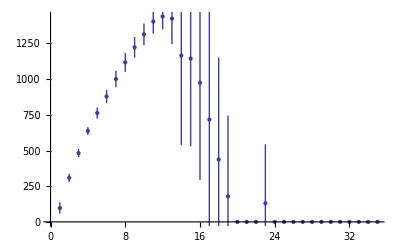
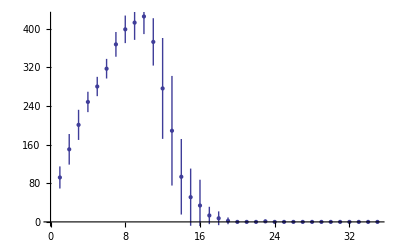
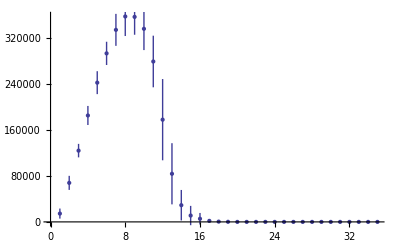
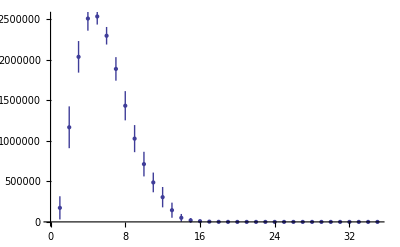
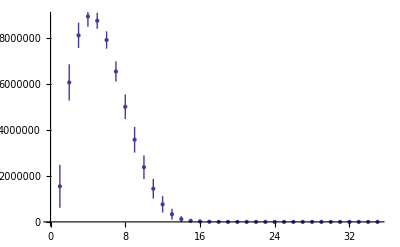
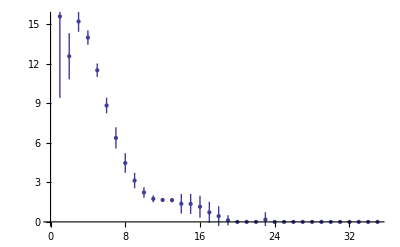
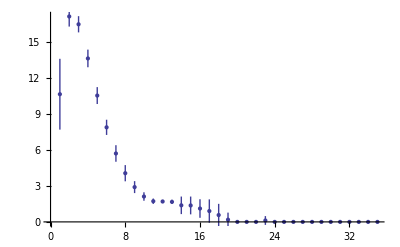
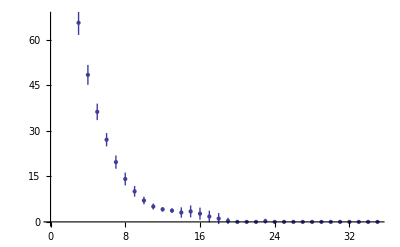
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
PlotDatafp=Partition[Riffle[mfpAll,SDfpAll],2];
PlotDatab=Partition[Riffle[mbAll,SDbAll],2];
PlotDataArea=Partition[Riffle[mAreaAll,SDAreaAll],2];
PlotDatatRed=Partition[Riffle[mtRedAll,SDtRedAll],2];
PlotDatatGreen=Partition[Riffle[mtGreenAll,SDtGreenAll],2];
PlotDatatBlue=Partition[Riffle[mtBlueAll,SDtBlueAll],2];

PlotDatacRed=Partition[Riffle[mcRedAll,SDcRedAll],2];
PlotDatacGreen=Partition[Riffle[mcGreenAll,SDcGreenAll],2];
PlotDatacBlue=Partition[Riffle[mcBlueAll,SDcBlueAll],2];


{frontposition, radius, area, red, green, blue,cRed,cGreen,cBlue}=
{ErrorListPlot[PlotDatafp],ErrorListPlot[PlotDatab],ErrorListPlot[PlotDataArea],ErrorListPlot[PlotDatatRed],ErrorListPlot[PlotDatatGreen],ErrorListPlot[PlotDatacBlue],ErrorListPlot[PlotDatacRed],ErrorListPlot[PlotDatacGreen],ErrorListPlot[PlotDatacBlue]}
```